(-(R2 (R5+Rf/2) Vcc)/(R4+R5+Rf)+(R2+R3) Vi)/R3

{{R2→150.,R5→111.538}}

{{x→0.513333}}

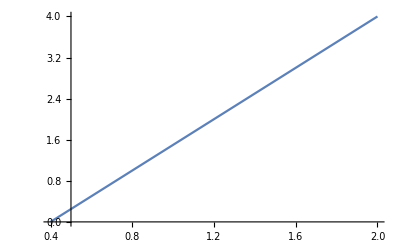

```mathematica
resistiveModel[Vcc_,Vi_, R2_, R3_, R4_, R5_, Rf_, Rx_]=Vo/.Solve[{
(Vo-Vi)/R2==(Vi-Voff)/R3/.{Voff->(R5+ Rf Rx)/(R4+Rf+R5)*Vcc}
}, {Vo}][[1]]//FullSimplify;
resistiveModel[Vcc, Vi, R2, R3, R4, R5, Rf, 1/2]
Reduce[{
resistiveModel[5, 4/10, R2, R3, R4, R5, Rf,1/2]==0,
resistiveModel[5, 2, R2, R3, R4, R5, Rf,1/2]==4
}, {R2, R3, R4, R5, Rf}];
Solve[Reduce[%/.{R3->100,R4->1000, Rf->100}, {R1, R5}]//N]

pot=Solve[resistiveModel[5, 0.4, 150, 100, 1000, 110, 100,x]==0,x]//N

Plot[resistiveModel[5, Vi, 150, 100, 1000, 110, 100,x]/.%, {Vi, 0.4, 2}]
```

```mathematica
resistorValue=0.4;
InputField[Dynamic[resistorValue]]

Dynamic[resistiveModel[5, resistorValue, 150, 100, 1000, 110, 100,x]/.pot]//N
```

```mathematica
10/1000*18000/100//N
```

1.8

```mathematica
Reduce[{(Vcc-V1)/R3==1/1000}/.{V1->R2/(R1+R2)Vcc}, {R1, R2, R3}]
```

R1+R2≠0&&R3==(1000 R1 Vcc)/(R1+R2)&&R1 Vcc≠0